```mathematica
TensorData = ToExpression[Import["C:\\ETH\\Neuro\\GlobalTracking\\GlobalTrackingScripts\\tensor_data.txt"]];
dim=Dimensions[TensorData]
Tensor[i_,j_,k_]:={{TensorData[[i,j,k,1]],TensorData[[i,j,k,2]],TensorData[[i,j,k,3]]},{TensorData[[i,j,k,2]],TensorData[[i,j,k,4]],TensorData[[i,j,k,5]]},{TensorData[[i,j,k,3]],TensorData[[i,j,k,5]],TensorData[[i,j,k,6]]}}
```

{9,9,9,6}

```mathematica
αmax = Pi/2.;
E0 = 2.;
```

```mathematica
g[{ϕ_,θ_}]:={Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}

S= Table[Eigenvectors[Tensor[i,j,k]][[1]],{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}];

A=Association[
Flatten[
Table[{i,j,k,1}->Association[{
"tensor"->Tensor[i,j,k],
"direction"->S[[i,j,k]],
"position" -> {i,j,k},
"neighbors"-> DeleteCases[
Flatten[
Table[{ii,jj,kk,1},
{ii,Max[1,i-1],Min[dim[[1]],i+1]},{jj,Max[1,j-1],Min[dim[[2]],j+1]},{kk,Max[1,k-1],Min[dim[[3]],k+1]}],
2],
{i,j,k,1}],
"forward"->{},
"backward"->{}}],
{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}],3]
];

AppendTo[A,
{}->Association[{
"tensor"->{},
"direction"->{},
"position" -> {},
"neighbors"-> {},
"forward"->{},
"backward"->{}}]
];
```

```mathematica
F[spin_]:=Select[
A[spin]["neighbors"],
( (A[#]["position"]-A[spin]["position"]).A[spin]["direction"]>0  )&
]

B[spin_]:=Select[
A[spin]["neighbors"],
( (A[#]["position"]-A[spin]["position"]).A[spin]["direction"]<=0  )&
]

Eint[{}]:=0

Eint[spin_]:=Module[{COSα = {}},
If[A[spin]["backward"]≠{},
AppendTo[COSα,Abs[(A[A[spin]["backward"]]["position"]-A[spin]["position"]).A[A[spin]["backward"]]["direction"]]];
AppendTo[COSα,Abs[(A[A[spin]["backward"]]["position"]-A[spin]["position"]).A[spin]["direction"]]];
];
If[A[spin]["forward"]≠{},
AppendTo[COSα, Abs[(A[A[spin]["forward"]]["position"]-A[spin]["position"]).A[A[spin]["forward"]]["direction"]]];AppendTo[COSα, Abs[(A[A[spin]["forward"]]["position"]-A[spin]["position"]).A[spin]["direction"]]];
];

E0 + Sum[-E0/4-Log[(cosα-Cos[αmax])/(1-Cos[αmax])],{cosα,COSα}]
]
```

```mathematica
Associate[spin_]:=Module[{newforward,newbackward,oldforward,oldbackward,E0,E1,p},

newforward= RandomChoice[F[spin]];(*What if newforward = {}? Should not happen for volume spins *)

oldforward =A[spin]["forward"];
oldbackward=A[newforward]["backward"];

E0 = Eint[spin] +  Eint[oldforward] +
	Eint[newforward] + Eint[oldbackward];

A[oldforward]["backward"] = {};
A[oldbackward]["forward"] = {};
A[spin]["forward"] = newforward;
A[newforward]["backward"] = spin;

E1 = Eint[spin] +  Eint[newforward] +
	Eint[oldforward] + Eint[oldbackward];

p = Min[1., Exp[E0-E1]];

If[RandomReal[{0,1}]> p,
A[oldforward]["backward"] = spin;
A[oldbackward]["forward"] = newforward;
A[spin]["forward"] = oldforward;
A[newforward]["backward"] = oldbackward;
];

(*========================================*)

newbackward= RandomChoice[B[spin]];

oldforward =A[newbackward]["forward"];
oldbackward=A[spin]["backward"];

E0 = Eint[spin] +  Eint[oldforward] +
	Eint[newbackward] + Eint[oldbackward];

A[oldforward]["backward"] = {};
A[oldbackward]["forward"] = {};
A[spin]["backward"] = newbackward;
A[newbackward]["forward"] = spin;

E1 = Eint[spin] +  Eint[newbackward] +
	Eint[oldforward] + Eint[oldbackward];

p = Min[1., Exp[E0-E1]];

If[RandomReal[{0,1}]> p,
A[oldforward]["backward"] = newbackward;
A[oldbackward]["forward"] = spin;
A[spin]["backward"] = oldbackward;
A[newbackward]["forward"] = oldforward;
];
]
```

```mathematica
Energy ={};
Block[{i,j,k,n},

For[n=1,n≤100,n++,

Energy = Append[Energy,Sum[Eint[{i,j,k,1}],{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}]];

For[i=2,i<dim[[1]],i++,
For[j=2,j<dim[[2]],j++,
For[k=2,k<dim[[3]],k++,
Associate[{i,j,k,1}];
]]]
];

]
```

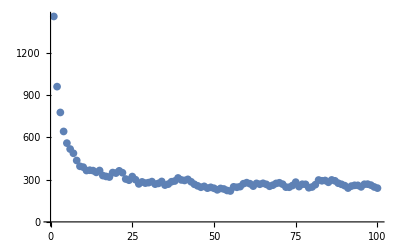

```mathematica
ListPlot[Energy,PlotRange->All]
```

```mathematica
Fiber[seed_,str_,fiber_]:=Module[{newfiber},

If[str == "forward",
If[seed =={},
fiber,
newfiber =Append[fiber,A[seed]["position"]];
Fiber[A[seed]["forward"],"forward",newfiber]
],

If[seed =={},
fiber,
newfiber =Append[fiber,A[seed]["position"]];
Fiber[A[seed]["backward"],"backward",newfiber]
]
]
]
```

```mathematica
Surface = Select[ Flatten[Table[{i,j,k,1},{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}],2], (#[[1]]==1 ||#[[1]]==dim[[1]] ||#[[2]]==1 ||#[[2]]==dim[[2]]||#[[3]]==1 ||#[[3]]==dim[[3]] )&];
```

```mathematica
Fibers = Join[Table[Fiber[surfacevoxel,"forward",{}],{surfacevoxel,Surface}],
Table[Fiber[surfacevoxel,"backward",{}],{surfacevoxel,Surface}]];

LongFibers=Select[Fibers,Length[#]>5&];

Graphics3D[{Thickness->0.005,
Table[Line[Fibers[[i]]],{i,1,Length[Fibers]}] 
}]
```

-Graphics3D-

```mathematica
Graphics3D[{Thickness->0.005,
Table[Line[LongFibers[[i]]],{i,1,Length[LongFibers]}] 
}]
```

-Graphics3D-